# MATURITETNE NALOGE

## 1. Največji skupni delitelj ,najmanjši skupini večkratnik in razcep številna prafaktorje

Za poljubni naravni števili p in q označimo z D (m, n) največji skupni delitelj teh dveh števil in z v (m, n) njun najmanjši skupini večkratnik.

a) Razcepite naslednja števila na prafaktorje: 32, 40, 72.

```mathematica
Prafaktorizacija[x_]:= FactorInteger[x]
a = 32
b = 40
c = 72
Prafaktorizacija[a]
Prafaktorizacija[b]
Prafaktorizacija[c]
```

32

40

72

{{2,5}}

{{2,3},{5,1}}

{{2,3},{3,2}}

b) Izračunajte : (D(32 ,40)/D(40, 72) - D(11,23)/v(4, 10)) * v(4,20)

```mathematica
NajvecjiSkupniDeljitelj[x_,y_]:=GCD[x,y]
NajmanjsiSkupniVečkratnik[t_,z_]:= LCM[t,z]

a = NajvecjiSkupniDeljitelj[32, 40]
b= NajvecjiSkupniDeljitelj[40, 72]
c=NajvecjiSkupniDeljitelj[11,23]
d=NajmanjsiSkupniVečkratnik[4,10]
e=NajmanjsiSkupniVečkratnik[4,20]
```

8

8

1

20

20

```mathematica
Rezultat =(a/b)-(c/d)*e
```

0

## 2. Risanje grafov

a)  Narišite graf funkcije f(x)= 2/-x.

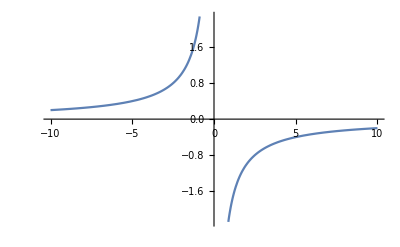

```mathematica
f[x_]:= 2/-x
Plot[f[x], {x,-10,10}]
```

b) Zapišite enačbo tangente na graf funkcije f v točki z absciso x0 = 1/2, ter jo nariši.

```mathematica
D[f[x],x]
```

2/x^2

```mathematica
ClearAll[b]
tangenta[x0_,gr_]:= Module[{k,n},
k= D[gr[b],b]/.{b->x0};
n= p/.Solve[f[x0]==k*x0+p,p];
k*x+n]
```

```mathematica
odvod[x_]=D[f[x],x]
```

2/x^2

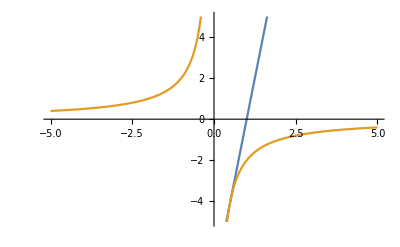

```mathematica
Plot[{tangenta[1/2,f],f[x]},{x,-5,5},PlotRange->{-5,5}]
```

```mathematica
Manipulate[Plot[{tangenta[x0,f],f[x]},{x,-5,5},PlotRange->{-5,5}],{x0,-4,4}]
```

## 3. Računanje nedoločenega integrala

a)  Izračunajte nedoločeni integral ∫((4 x^2-3)/x+(x^2)^(1/3)-e^x+3)ⅆx.

```mathematica
ClearAll[x]
```

```mathematica
Integrate[(4x^2-3)-3+CubeRoot[x^2]-E^x+3,x]
```

-ⅇ^x-3 x+(4 x^3)/3+3/5 x (x^2)^(1/3)

Odgovor: Rešitev naloge je -ⅇ^x-3 x+(4 x^3)/3+3/5 x (x^2)^(1/3).

## 4. Vektorji

V prostoru R^3 so dani vektorji a = (1, 2,- 1)  , b =  (x, -2, -1)  in c = (1, 1, 2).

a) Računsko pokažite, da sta vektorja a in b pravokotna in izračunaj x.

```mathematica
ClearAll[x,a,b,c]
```

```mathematica
a = {1,2,-1}
b = {x,-2,-1}
c = {1,1,2}
```

{1,2,-1}

{x,-2,-1}

{1,1,2}

```mathematica
Solve[Dot[a,b] ==0,x]
```

{{x→3}}

Odgovor: x je 3.

b) Izračunaj vektorski produkt od b in c.

```mathematica
x = 3
Cross[{x,-2,-1},{1,1,2}]
```

3

{-3,-7,5}

Odgovor: Vektorski produkt je {-3,-7,5}.

c) Izračunaj 3a + 4b - c/2.

```mathematica
Simplify[3*a+4*b-c/2]
```

{29/2,-5/2,-8}

d) Izračunaj Normo danih vektorjev.

```mathematica
Norm[a]
Norm[b]
Norm[c]
```

√6

√14

√6

Odgovor: Dolžine vektorje √6, √14 in √6.

## 5. Risanje Stožnic

Dan je pravokotnik ABCD z oglišči  A(-3, -2), B(3, -2),C(3, 2)in D (-3, 2).

a) Zapišite enačbo elipse v središčni legi,ki je včrtana v pravokotnik ABCD in se dotika vseh štirih njegovih stranic.

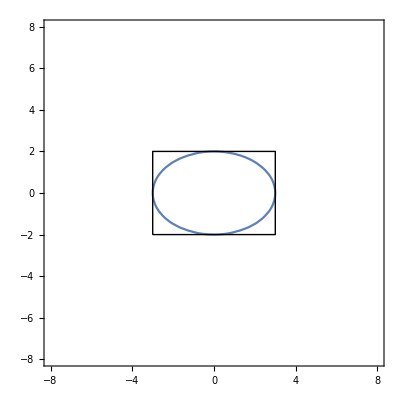

```mathematica
Show[ContourPlot[{x^2/3^2+y^2/2^2==1}, {x,-8,8}, {y, -8, 8}],Graphics[Line[{{-3,-2},{3,-2},{3,-2},{3,2},{3,2},{-3,2},{-3,2},{-3,-2}}]]]
```

b) Zapišite enačbo hiperbole v središčni legi, ki ima teme v točki T(0, 2) njeni asimptoti pa sta nosilki diagonal pravokotnika ABCD

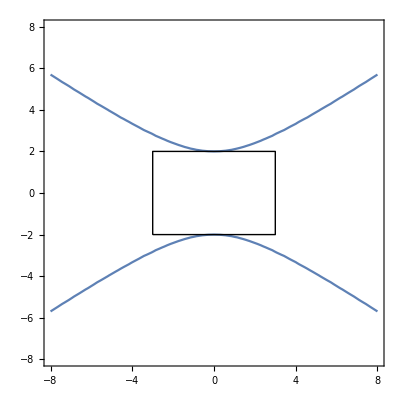

```mathematica
Show[ContourPlot[{x^2/3^2-y^2/2^2==-1}, {x,-8,8}, {y, -8, 8}],Graphics[Line[{{-3,-2},{3,-2},{3,-2},{3,2},{3,2},{-3,2},{-3,2},{-3,-2}}]]]
```

c) Zapišite enačbo krožnice, ki ima središče v točki C in poteka skozi točko A.

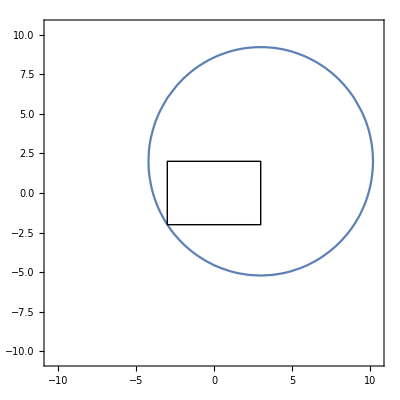

```mathematica
Show[ContourPlot[{(x-3)^2+(y-2)^2==52}, {x,-10.5,10.5}, {y, -10.5, 10.5}],Graphics[Line[{{-3,-2},{3,-2},{3,-2},{3,2},{3,2},{-3,2},{-3,2},{-3,-2}}]]]
```